```mathematica
StringJoin@@Table[ToString@Table[spc[k,l],{l,0,k}]<>"\n",{k,0,20}]
```

{1}
{1, 1}
{1, 2, 2}
{1, 3, 5, 5}
{1, 4, 9, 14, 14}
{1, 5, 14, 28, 42, 42}
{1, 6, 20, 48, 90, 132, 132}
{1, 7, 27, 75, 165, 297, 429, 429}
{1, 8, 35, 110, 275, 572, 1001, 1430, 1430}
{1, 9, 44, 154, 429, 1001, 2002, 3432, 4862, 4862}
{1, 10, 54, 208, 637, 1638, 3640, 7072, 11934, 16796, 16796}
{1, 11, 65, 273, 910, 2548, 6188, 13260, 25194, 41990, 58786, 58786}
{1, 12, 77, 350, 1260, 3808, 9996, 23256, 48450, 90440, 149226, 208012, 208012}
{1, 13, 90, 440, 1700, 5508, 15504, 38760, 87210, 177650, 326876, 534888, 742900, 742900}
{1, 14, 104, 544, 2244, 7752, 23256, 62016, 149226, 326876, 653752, 1188640, 1931540, 2674440, 2674440}
{1, 15, 119, 663, 2907, 10659, 33915, 95931, 245157, 572033, 1225785, 2414425, 4345965, 7020405, 9694845, 9694845}
{1, 16, 135, 798, 3705, 14364, 48279, 144210, 389367, 961400, 2187185, 4601610, 8947575, 15967980, 25662825, 35357670, 35357670}
{1, 17, 152, 950, 4655, 19019, 67298, 211508, 600875, 1562275, 3749460, 8351070, 17298645, 33266625, 58929450, 94287120, 129644790, 129644790}
{1, 18, 170, 1120, 5775, 24794, 92092, 303600, 904475, 2466750, 6216210, 14567280, 31865925, 65132550, 124062000, 218349120, 347993910, 477638700, 477638700}
{1, 19, 189, 1309, 7084, 31878, 123970, 427570, 1332045, 3798795, 10015005, 24582285, 56448210, 121580760, 245642760, 463991880, 811985790, 1289624490, 1767263190, 1767263190}
{1, 20, 209, 1518, 8602, 40480, 164450, 592020, 1924065, 5722860, 15737865, 40320150, 96768360, 218349120, 463991880, 927983760, 1739969550, 3029594040, 4796857230, 6564120420, 6564120420}

```mathematica
And@@Table[And@@Table[spc[k,l]==((k+l)!(k-l+1))/(l!(k+1)!),{l,0,k}],{k,0,20}]
```

True

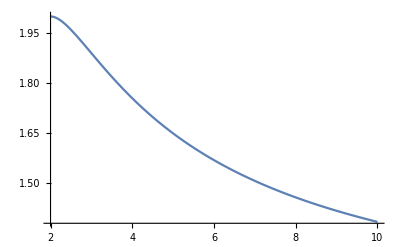

```mathematica
Plot[β/(β-1)^((β-1)/β),{β,2,10}]
```

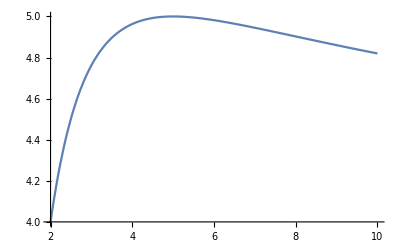

```mathematica
Plot[β/(β-1)^((β-1)/β)4^((β-1)/β),{β,2,10},PlotRange->Full]
```

```mathematica
Limit[β/(β-1)^((β-1)/β)4^((β-1)/β),β->∞]
```

4

```mathematica
β/(β-1)^((β-1)/β)4^((β-1)/β)/.β->2
```

4

```mathematica
D[β/(β-1)^((β-1)/β)4^((β-1)/β),β]
```

4^((-1+β)/β) (-1+β)^(-(-1+β)/β)+4^((-1+β)/β) (-(-1+β)/β^2+1/β) (-1+β)^(-(-1+β)/β) β Log[4]+4^((-1+β)/β) (-1+β)^(-(-1+β)/β) β (-1/β+((-1+β)/β^2-1/β) Log[-1+β])

```mathematica
Solve[4^((-1+β)/β) (-1+β)^(-(-1+β)/β)+4^((-1+β)/β) (-(-1+β)/β^2+1/β) (-1+β)^(-(-1+β)/β) β Log[4]+4^((-1+β)/β) (-1+β)^(-(-1+β)/β) β (-1/β+((-1+β)/β^2-1/β) Log[-1+β])==0,β]
```

{{β→5}}

```mathematica
β/(β-1)^((β-1)/β)4^((β-1)/β)/.β->5
```

5